slightly longer

```mathematica
ClearAll["Global`*"]
```

```mathematica
colRll=ColorData[90, "ColorList"][[2]]
colRtd =ColorData[70, "ColorList"][[3]]
colRin=ColorData[51, "ColorList"][[1]]
colDll =ColorData[93, "ColorList"][[2]]
colDav=ColorData[33, "ColorList"][[3]]
colCoa=ColorData[21, "ColorList"][[3]]
colCll=ColorData[90, "ColorList"][[1]]
colCln =ColorData[66, "ColorList"][[2]]
colCon =ColorData[26, "ColorList"][[2]]
colNor=ColorData[55, "ColorList"][[1]]
```

Hue[0.01, 0.8, 0.8]

Hue[0.5, 0.5, 0.5]

RGBColor[1, 0.753262, 0.0437629]

Hue[0.11, 0.75, 0.92]

RGBColor[0.8509803921568627, 0.7333333333333333, 0.592156862745098]

RGBColor[1., 0.35294117647058826, 0.12156862745098039]

Hue[0.22, 1, 0.6]

Hue[0.17, 0.4, 0.65]

RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393]

RGBColor[0.709133, 0.747539, 0.83711]

```mathematica
SigI:={{1,0},{0,1}};(*Pauli matrices*)
SigZ:={{-1,0},{0,1}};
SigX:={{0,1},{1,0}};
SigY:={{0,-I},{I,0}};
```

```mathematica
c=2
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];(*Tensor products*)
```

2

```mathematica
H= 0.5 At[SigZ,1] -0.7  At[SigZ,2] + 0.3At[SigZ,1]. At[SigZ,2] + At[SigX,1] +At[SigX,2]  ;(*Some Hamiltonian - adiabatic will come later. Earlier comment: 0.98 is the turnaround, imaginary at 0.31ish - two small ones collided         !*)
A = At[SigZ,1];
```

```mathematica
{Es,S} =Eigensystem[H];
Sd = Transpose[S];
Ainbasis =S.A.Sd;
rhoIn= (At[SigZ,2] + At[SigZ,1].At[SigZ,2])/4 +(At[SigZ,1] + At[SigI,1])/4;
```

```mathematica
beeta=4; (*used to be 4*)
al=1.01;
bl=0.6;
SpDen0 =3(Exp[ - (bl Abs[ beeta dE]) +0.5 beeta dE] - (1/al) Exp[ - (al bl Abs[ beeta dE]) +0.5 beeta dE]);
corfunk0 =(1/(2 Pi))Integrate[Exp[-I t dE ]SpDen0  , {dE,-Infinity,Infinity},Assumptions->t>0];
overt120 =NIntegrate[Abs[ corfunk0], {t,0,Infinity}];
```

```mathematica
t12 =10;
normaliz =1/(t12 overt120 );
SpDen =3normaliz ( Exp[ -bl  Abs[ beeta dE] +0.5 beeta dE] -(1/al) Exp[ - al bl Abs[ beeta dE] +0.5 beeta dE]);
corfunk =(1/(2 Pi))Integrate[Exp[-I t dE ]SpDen  , {dE,-Infinity,Infinity},Assumptions->t>0];
overt12 =NIntegrate[Abs[ corfunk], {t,0,Infinity}];
t12 = (1/overt12);
tbath =t12 NIntegrate[t Abs[ corfunk], {t,0,Infinity}]
```

0.685796

this code takes 922 seconds:

```mathematica
(*Timing[ftdA=Table[Ainbasis[[i,j]]Integrate[ Conjugate[corfunk] Exp[-I(Es[[i]]- Es[[j]])t],{t,0,x},Assumptions->x>0],{i,1,2^c},{j,1,2^c}];]*)
```

and produces this:

```mathematica
ftdA={{(-0.31362269158068795+0. ⅈ) ((0.+0.13684410151692772 ⅈ)-1.7816354603545073 ArcTan[0.22603978300179436 x]+1.7994518149584582 ArcTan[0.22727272727274128 x]-1.7816354603953082 ArcTan[2.3584905660377427 x]+1.7994518149992587 ArcTan[2.4999999999999925 x]+(0.+0.8997259074996298 ⅈ) Log[0.16000000000000095+1. x^2]-(0.+0.8908177301976541 ⅈ) Log[0.17977599999999896+1. x^2]-(0.+0.8997259074792293 ⅈ) Log[19.359999999997612+1. x^2]+(0.+0.8908177301772536 ⅈ) Log[19.571776000002416+1. x^2]),-0.037374102010989924 ((-2.281737025854867+0.020870993820033247 ⅈ)-(0.+7.3840693802688975 ⅈ) ExpIntegralEi[(-2.005001329879431+0. ⅈ)+(0.+4.72877672141377 ⅈ) x]+(0.+6.657769927267695 ⅈ) ExpIntegralEi[(-1.8915106885655117+0. ⅈ)+(0.+4.72877672141377 ⅈ) x]-(0.+9.239679970785231*^-10 ⅈ) ExpIntegralEi[(20.806617574219374+0. ⅈ)+(0.+4.72877672141377 ⅈ) x]+(0.+8.166711165374379*^-10 ⅈ) ExpIntegralEi[(20.920108215535674+0. ⅈ)+(0.+4.72877672141377 ⅈ) x]),-0.423078157410798 ((-0.5498078242044235+0.02897361992275571 ⅈ)-(0.+3.2009250344113798 ⅈ) ExpIntegralEi[(-1.169116277980888+0. ⅈ)+(0.+2.757349712219086 ⅈ) x]+(0.+3.025915768465912 ⅈ) ExpIntegralEi[(-1.1029398848876364+0. ⅈ)+(0.+2.757349712219086 ⅈ) x]-(0.+5.405655489209197*^-6 ⅈ) ExpIntegralEi[(12.13233873376327+0. ⅈ)+(0.+2.757349712219086 ⅈ) x]+(0.+5.009414261505529*^-6 ⅈ) ExpIntegralEi[(12.198515126857908+0. ⅈ)+(0.+2.757349712219086 ⅈ) x]),0.7098092169088376 ((-0.35793715574871365+0.0322643362993732 ⅈ)-(0.+2.6090018134009365 ⅈ) ExpIntegralEi[(-0.9646441379055591+0. ⅈ)+(0.+2.2751040988338747 ⅈ) x]+(0.+2.4950668780936134 ⅈ) ExpIntegralEi[(-0.9100416395335515+0. ⅈ)+(0.+2.2751040988338747 ⅈ) x]-(0.+0.00004512003654912341 ⅈ) ExpIntegralEi[(10.010458034868464+0. ⅈ)+(0.+2.2751040988338747 ⅈ) x]+(0.+0.00004229942903653821 ⅈ) ExpIntegralEi[(10.065060533241615+0. ⅈ)+(0.+2.2751040988338747 ⅈ) x])},{-0.037374102010989924 ((-3.7410381310768604*^8-0.02624006409591879 ⅈ)+(0.+1.210660334657599*^9 ⅈ) ExpIntegralEi[(-20.920108215535674+0. ⅈ)-(0.+4.72877672141377 ⅈ) x]-(0.+1.0915793924863691*^9 ⅈ) ExpIntegralEi[(-20.806617574219374+0. ⅈ)-(0.+4.72877672141377 ⅈ) x]+(0.+0.15148982857465224 ⅈ) ExpIntegralEi[(1.8915106885655117+0. ⅈ)-(0.+4.72877672141377 ⅈ) x]-(0.+0.13389789239179714 ⅈ) ExpIntegralEi[(2.005001329879431+0. ⅈ)-(0.+4.72877672141377 ⅈ) x]),(0.17785689443203118+0. ⅈ) ((0.+0.13684410151692772 ⅈ)-1.7816354603545073 ArcTan[0.22603978300179436 x]+1.7994518149584582 ArcTan[0.22727272727274128 x]-1.7816354603953082 ArcTan[2.3584905660377427 x]+1.7994518149992587 ArcTan[2.4999999999999925 x]+(0.+0.8997259074996298 ⅈ) Log[0.16000000000000095+1. x^2]-(0.+0.8908177301976541 ⅈ) Log[0.17977599999999896+1. x^2]-(0.+0.8997259074792293 ⅈ) Log[19.359999999997612+1. x^2]+(0.+0.8908177301772536 ⅈ) Log[19.571776000002416+1. x^2]),0.8191476789389398 ((-702.7301275346462+0.021606309142302677 ⅈ)+(0.+6099.222920484327 ⅈ) ExpIntegralEi[(-8.721593088677764+0. ⅈ)-(0.+1.9714270091946844 ⅈ) x]-(0.+5875.536973570854 ⅈ) ExpIntegralEi[(-8.674278840456104+0. ⅈ)-(0.+1.9714270091946844 ⅈ) x]+(0.+0.4564405079703547 ⅈ) ExpIntegralEi[(0.7885708036778752+0. ⅈ)-(0.+1.9714270091946844 ⅈ) x]-(0.+0.4310369384054441 ⅈ) ExpIntegralEi[(0.835885051898543+0. ⅈ)-(0.+1.9714270091946844 ⅈ) x]),0.47544013200761037 ((-7727.394979107484+0.008789049315602622 ⅈ)+(0.+51501.75921476231 ⅈ) ExpIntegralEi[(-10.855047682294057+0. ⅈ)-(0.+2.4536726225798957 ⅈ) x]-(0.+49042.05299846541 ⅈ) ExpIntegralEi[(-10.79615953935091+0. ⅈ)-(0.+2.4536726225798957 ⅈ) x]+(0.+0.3763652660544591 ⅈ) ExpIntegralEi[(0.9814690490319601+0. ⅈ)-(0.+2.4536726225798957 ⅈ) x]-(0.+0.3513284884378401 ⅈ) ExpIntegralEi[(1.0403571919738719+0. ⅈ)-(0.+2.4536726225798957 ⅈ) x])},{-0.423078157410798 ((-33901.42664981974+0.0017487138672251448 ⅈ)+(0.+197370.64567609984 ⅈ) ExpIntegralEi[(-12.198515126857908+0. ⅈ)-(0.+2.757349712219086 ⅈ) x]-(0.+186579.4864177276 ⅈ) ExpIntegralEi[(-12.13233873376327+0. ⅈ)-(0.+2.757349712219086 ⅈ) x]+(0.+0.3333154331267433 ⅈ) ExpIntegralEi[(1.1029398848876364+0. ⅈ)-(0.+2.757349712219086 ⅈ) x]-(0.+0.30888299996523466 ⅈ) ExpIntegralEi[(1.169116277980888+0. ⅈ)-(0.+2.757349712219086 ⅈ) x]),0.8191476789389398 ((-0.2642829140333951+0.03486932348339758 ⅈ)-(0.+2.2937972113257783 ⅈ) ExpIntegralEi[(-0.835885051898543+0. ⅈ)+(0.+1.9714270091946844 ⅈ) x]+(0.+2.209673347039488 ⅈ) ExpIntegralEi[(-0.7885708036778752+0. ⅈ)+(0.+1.9714270091946844 ⅈ) x]-(0.+0.0001716582551458025 ⅈ) ExpIntegralEi[(8.674278840456104+0. ⅈ)+(0.+1.9714270091946844 ⅈ) x]+(0.+0.00016210447464246774 ⅈ) ExpIntegralEi[(8.721593088677764+0. ⅈ)+(0.+1.9714270091946844 ⅈ) x]),(-0.0699164064500365+0. ⅈ) ((0.+0.13684410151692772 ⅈ)-1.7816354603545073 ArcTan[0.22603978300179436 x]+1.7994518149584582 ArcTan[0.22727272727274128 x]-1.7816354603953082 ArcTan[2.3584905660377427 x]+1.7994518149992587 ArcTan[2.4999999999999925 x]+(0.+0.8997259074996298 ⅈ) Log[0.16000000000000095+1. x^2]-(0.+0.8908177301976541 ⅈ) Log[0.17977599999999896+1. x^2]-(0.+0.8997259074792293 ⅈ) Log[19.359999999997612+1. x^2]+(0.+0.8908177301772536 ⅈ) Log[19.571776000002416+1. x^2]),-0.3664808526358411 ((-0.042790667213441366+0.06799139620820281 ⅈ)+(0.+8.396191052668415 ⅈ) ExpIntegralEi[(-2.1334545936162925+0. ⅈ)-(0.+0.4822456133852113 ⅈ) x]-(0.+8.382570360257976 ⅈ) ExpIntegralEi[(-2.1218806988948056+0. ⅈ)-(0.+0.4822456133852113 ⅈ) x]+(0.+0.8280975221183557 ⅈ) ExpIntegralEi[(0.1928982453540849+0. ⅈ)-(0.+0.4822456133852113 ⅈ) x]-(0.+0.8104638209270233 ⅈ) ExpIntegralEi[(0.20447214007532882+0. ⅈ)-(0.+0.4822456133852113 ⅈ) x])},{0.7098092169088376 ((-3206.7670041341144+0.013304917509665498 ⅈ)+(0.+23374.105744982073 ⅈ) ExpIntegralEi[(-10.065060533241615+0. ⅈ)-(0.+2.2751040988338747 ⅈ) x]-(0.+22353.360104878207 ⅈ) ExpIntegralEi[(-10.010458034868464+0. ⅈ)-(0.+2.2751040988338747 ⅈ) x]+(0.+0.404231419136099 ⅈ) ExpIntegralEi[(0.9100416395335515+0. ⅈ)-(0.+2.2751040988338747 ⅈ) x]-(0.+0.37896153318651216 ⅈ) ExpIntegralEi[(0.9646441379055591+0. ⅈ)-(0.+2.2751040988338747 ⅈ) x]),0.47544013200761037 ((-0.42224760007398693+0.03094408505920431 ⅈ)-(0.+2.814207671256753 ⅈ) ExpIntegralEi[(-1.0403571919738719+0. ⅈ)+(0.+2.4536726225798957 ⅈ) x]+(0.+2.6798020857358233 ⅈ) ExpIntegralEi[(-0.9814690490319601+0. ⅈ)+(0.+2.4536726225798957 ⅈ) x]-(0.+0.000020565705619203618 ⅈ) ExpIntegralEi[(10.79615953935091+0. ⅈ)+(0.+2.4536726225798957 ⅈ) x]+(0.+0.000019197622417701956 ⅈ) ExpIntegralEi[(10.855047682294057+0. ⅈ)+(0.+2.4536726225798957 ⅈ) x]),-0.3664808526358411 ((-0.006217311438552488+0.06430634074495428 ⅈ)-(0.+1.2199327123102217 ⅈ) ExpIntegralEi[(-0.20447214007532882+0. ⅈ)+(0.+0.4822456133852113 ⅈ) x]+(0.+1.217953680613847 ⅈ) ExpIntegralEi[(-0.1928982453540849+0. ⅈ)+(0.+0.4822456133852113 ⅈ) x]-(0.+0.12031923164159185 ⅈ) ExpIntegralEi[(2.1218806988948056+0. ⅈ)+(0.+0.4822456133852113 ⅈ) x]+(0.+0.11775712594560174 ⅈ) ExpIntegralEi[(2.1334545936162925+0. ⅈ)+(0.+0.4822456133852113 ⅈ) x]),(0.2056822035986929+0. ⅈ) ((0.+0.13684410151692772 ⅈ)-1.7816354603545073 ArcTan[0.22603978300179436 x]+1.7994518149584582 ArcTan[0.22727272727274128 x]-1.7816354603953082 ArcTan[2.3584905660377427 x]+1.7994518149992587 ArcTan[2.4999999999999925 x]+(0.+0.8997259074996298 ⅈ) Log[0.16000000000000095+1. x^2]-(0.+0.8908177301976541 ⅈ) Log[0.17977599999999896+1. x^2]-(0.+0.8997259074792293 ⅈ) Log[19.359999999997612+1. x^2]+(0.+0.8908177301772536 ⅈ) Log[19.571776000002416+1. x^2])}};
```

```mathematica
t12factor=tbath;
t12=t12factor 10 ;
normaliz =1/(t12 overt120 );
SpDen =3normaliz ( Exp[ -bl  Abs[ beeta dE] +0.5 beeta dE] -(1/al) Exp[ - al bl Abs[ beeta dE] +0.5 beeta dE]);
corfunk =(1/(2 Pi))Integrate[Exp[-I t dE ]SpDen  , {dE,-Infinity,Infinity},Assumptions->t>0];
overt12 =NIntegrate[Abs[ corfunk], {t,0,Infinity}];
t12 = (1/overt12);
tbath =t12 NIntegrate[t Abs[ corfunk], {t,0,Infinity}];
sol = NDSolve[{rhoMat'[x] == ( I*(rhoMat[x].S.H.Sd -S.H.Sd.rhoMat[x])  + (1/t12factor)(Ainbasis.rhoMat[x].ftdA +Conjugate[Transpose[ftdA]].rhoMat[x].Ainbasis -rhoMat[x].ftdA.Ainbasis-Ainbasis.Conjugate[Transpose[ftdA]].rhoMat[x])), 
   rhoMat[0] == S.rhoIn.Sd}, {rhoMat}, {x, 0,3.0t12},MaxSteps->100000];
SolORedfield  =rhoMat /. sol[[1,1]];
```

confirming positivity of the solution:

```mathematica
Re[Eigenvalues[SolORedfield[2.56t12]]]
```

{0.770309,0.169044,0.060563,0.0000841276}

```mathematica
timeConst = 2.56 ;
```

This takes an hour:

```mathematica
(*Timing[justmaxNormTable6=Table[
potenMax=0;
precalc=(ftdA/.x->(timeConst t12 tLimit/100));
For[m=1,m<300000,m++,
randMat = RandomVariate[GaussianUnitaryMatrixDistribution[2^c]];
{evalues, evec}=Eigensystem[randMat];
randDenMat= (1/Total[Abs[evalues]])Transpose[evec].Abs[Chop[Conjugate[evec].randMat.Transpose[evec]]].Conjugate[evec];

matRHS =(1/t12factor)(Ainbasis.randDenMat.precalc  +ConjugateTranspose[precalc].randDenMat.Ainbasis -randDenMat.precalc.Ainbasis-Ainbasis.ConjugateTranspose[precalc].randDenMat);
candidMax=Total[Abs[Eigenvalues[matRHS ]]];
If[candidMax>potenMax,potenMax=candidMax,0];
];
potenMax,{tLimit,1,100}];]*)
```

and evaluates to:

```mathematica
justmaxNormTable6={0.13625277658247434,0.2271261344323564,0.28727220371273887,0.33250075951551983,0.37029397627774663,0.40271754332189424,0.40736594015237887,0.4180157958878515,0.41860082347820327,0.43447242500347016,0.4195251202025071,0.4059369283625248,0.41226636665407357,0.408973506686298,0.4183873286714153,0.4195517010133962,0.401094534970432,0.401155274225066,0.413560748746326,0.4231838472412014,0.40873350800205266,0.42933439966666376,0.4237282137451651,0.4083252161470393,0.41293133259795667,0.4102754192049166,0.4256014331887795,0.40026223764204594,0.4129022480082211,0.41210834427859494,0.4153898179708457,0.4037183147082594,0.421782077126944,0.4126848644186196,0.4050789600131528,0.4091116325314532,0.41872224846964234,0.4061493257980902,0.40467090710900866,0.42084714692887154,0.40874710912888246,0.40760977891683914,0.4198083866915851,0.408875129709536,0.40234178980270807,0.40492563750766025,0.4090303549988218,0.41905118707215583,0.41478640675597195,0.41578211939801946,0.4191110585031859,0.40632719851988364,0.4125404241195417,0.4066260107072258,0.40862103701067976,0.4134745819147972,0.4134943846835991,0.40536129477936683,0.4053602826787508,0.4174292619400807,0.42382693416697304,0.41190946156765346,0.4126215243665926,0.4249809424641092,0.4184781069055633,0.4177719957178938,0.41288195349517276,0.4183794867645572,0.43769373898380803,0.41985704400941815,0.4066249406963439,0.41287201323125466,0.4151571814386592,0.4144238051631125,0.40615909870455735,0.41440359539072485,0.42245499124682556,0.4224370154279492,0.40468432425134093,0.4149066713080723,0.41053925472608,0.4115861709600311,0.41143142473472477,0.4165591316686071,0.41646587975266974,0.41886210290025316,0.40722391754742965,0.42317839274224434,0.41156868425013915,0.4078385937317991,0.42438270358532443,0.418301606199013,0.4111458531544227,0.4124354847298125,0.4120240671142553,0.4071288205436841,0.41221409174985346,0.41680648014423394,0.4086568943784156,0.4150229124932491};
```

```mathematica
Max[justmaxNormTable6]
```

0.437694

we believe this bruteforce search finds the maximum norm of the r.h.s to 0.01 precision, which results in 3% accuracy in t12effective, and 1.5% accuracy in Tave for CGME. That is enough for making the choice of Tave. The analysis that leads to a 0.01 error bar on the computation below involves extrapolation to infinite number of samples (the convergence to the true maximum is weaker than any polinomial in the number of samples) and is not presented here.

We have tried more sophisticated optimization methods like Monte-Carlo or Simulated Annealing, but did not observe a significant improvement in the runtime. We proceed using the obtained value to adjust t12:

```mathematica
t12effective =4/Max[justmaxNormTable6];
boostEffective = Sqrt[t12effective/t12]
```

1.15438

```mathematica
filterRedplus=Integrate[Conjugate[corfunk] Exp[-y I t],{t,0,Infinity},Assumptions-> y >0];
filterRedminus=Integrate[Conjugate[corfunk] Exp[-y I t],{t,0,Infinity},Assumptions-> y <0];
zeMat={{0,0},{0,0}};
zeInit =At[zeMat,1];
termsL=I*(pMat[x].S.H.Sd -S.H.Sd.pMat[x]) ;
For[i=1,i<2^c +1,i++,
For[j=1,j<2^c +1,j++,
If[(i==j)&&(i<2^c),0,a=zeInit;
If[(i==j)&&(i==2^c),For[m=1,m<2^c +1,m++,
a[[m,m]] = Ainbasis[[m,m]] ;
];,a[[i,j]] = Ainbasis[[i,j]] ;
];
ad = ConjugateTranspose[a];
termsL=termsL+Re[If[(Es[[j]]- Es[[i]] + 0.00000001)>0,filterRedplus /.y->(Es[[j]]- Es[[i]] + 0.00000001),filterRedminus/.y->(Es[[j]]- Es[[i]] )]](2 a.pMat[x].ad  - ad.a.pMat[x] - pMat[x].ad. a   ) -I Im[If[(Es[[j]]- Es[[i]] + 0.00000001)>0,filterRedplus /.y->(Es[[j]]- Es[[i]] + 0.00000001),filterRedminus/.y->(Es[[j]]- Es[[i]] )]] ( -ad.a.pMat[x] + pMat[x].ad. a ) ;]]];
pIn =S.rhoIn.Sd;
s = NDSolve[{pMat'[x] == termsL, 
   pMat[0] == pIn}, {pMat}, {x, 0, timeConst t12}];
Lindsol =pMat/.s[[1,1]];
denmatDif2=SolORedfield[x t12]-Lindsol[x t12];
traceNorm2=Re[Tr[MatrixPower[denmatDif2.ConjugateTranspose[denmatDif2 ],1/2]]];
sol = NDSolve[{rhoMat'[x] == I*(rhoMat[x].S.H.Sd -S.H.Sd.rhoMat[x]) , 
   rhoMat[0] == S.rhoIn.Sd}, {rhoMat}, {x, 0,timeConst t12}];
SolIsol  =rhoMat /. sol[[1,1]];
denmatDifISca=SolORedfield[t12 x]-SolIsol[t12 x];
traceNormISca=Re[Tr[MatrixPower[denmatDifISca.ConjugateTranspose[denmatDifISca ],1/2]]];


davNo = NIntegrate[traceNorm2,{x,0,timeConst }]/timeConst ;
```

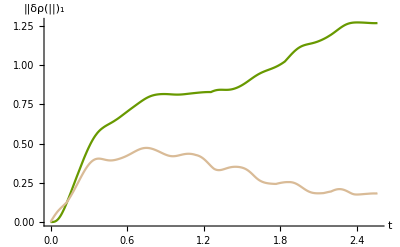
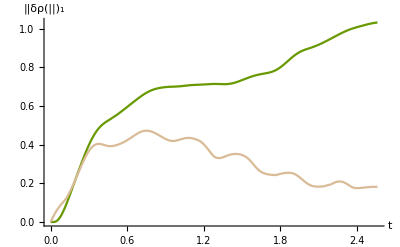
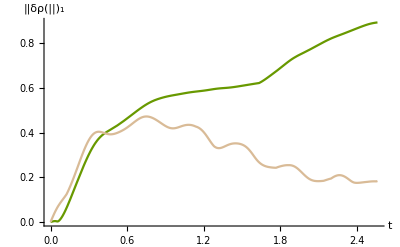
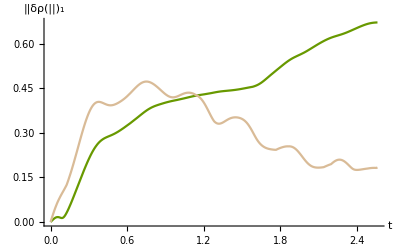
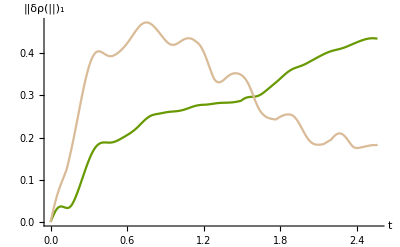
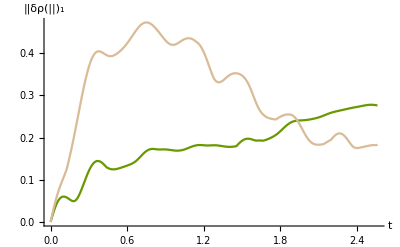
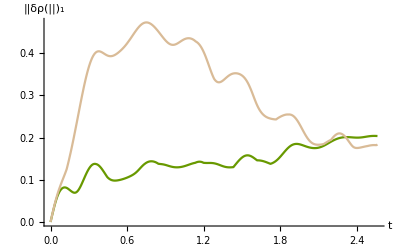
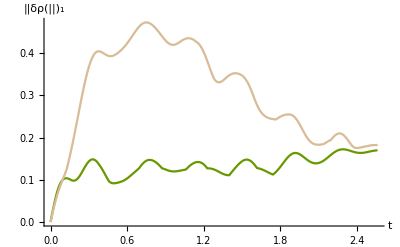
{{0.0447834,0.842206,-Graphics-},{0.179134,0.691834,-Graphics-},{0.403051,0.574129,-Graphics-},{0.716535,0.422403,-Graphics-},{1.11959,0.275196,-Graphics-},{1.6122,0.181866,-Graphics-},{2.19439,0.14258,-Graphics-},{2.86614,0.131495,-Graphics-},{3.62746,0.131518,-Graphics-},{4.47834,0.136776,-Graphics-},{5.41879,0.142029,-Graphics-},{6.44881,0.149086,-Graphics-},{7.5684,0.16172,-Graphics-},{8.77755,0.180339,-Graphics-},{10.0763,0.202086,-Graphics-},{11.4646,0.223541,-Graphics-},{12.9424,0.241849,-Graphics-},{14.5098,0.258423,-Graphics-},{16.1668,0.273862,-Graphics-},{17.9134,0.285996,-Graphics-},{19.7495,0.294677,-Graphics-},{21.6752,0.303325,-Graphics-}}

```mathematica
avNoList=Table[0,{j,1,22},{i,1,2}];
ErrorVaryTave =Table[
factorTave=itirador^2/25.0;
Tave = factorTave boostEffective Sqrt[t12 tbath/5];

filter2=(Sin[Tave(eps - omeg)/2])/(Tave(eps - omeg)/2);


Hls =Table[Sum[omP =Es[[k]]-Es[[i]]; om = Es[[j]]-Es[[k]];If[om +omP ==0,(1/(Tave  ))Re[NIntegrate[I(t-Tave) Exp[I om t ] corfunk,{t,0,Tave}]]Ainbasis[[i,k]]Ainbasis[[k,j]],(1/(Tave (om + omP) ))Re[NIntegrate[(Exp[I(om t - Tave (om +omP)/2)] - Exp[-I(omP t - Tave (om +omP)/2)])corfunk,{t,0,Tave}]]Ainbasis[[i,k]]Ainbasis[[k,j]]],{k,1,2^c}],{i,1,2^c},{j,1,2^c}];

zeMat={{0,0},{0,0}};
zeInit =At[zeMat,1];
termsC=I*(pMat[x].S.H.Sd -S.H.Sd.pMat[x])  ;
For[i=1,i<2^c +1,i++,
For[j=1,j<2^c +1,j++,
If[(i==j)&&(i<2^c),0,
a=zeInit;
If[(i==j)&&(i==2^c),For[m=1,m<2^c +1,m++,
a[[m,m]] = Ainbasis[[m,m]] ;
];,a[[i,j]] = Ainbasis[[i,j]] ;
];
ad = ConjugateTranspose[a];
For[k=1,k<2^c +1,k++,
For[l=1,l<2^c +1,l++,
If[(k==l )&&(k<2^c),0,
b=zeInit;

If[(k==l)&&(k==2^c),For[m=1,m<2^c +1,m++,
b[[m,m]] = Ainbasis[[m,m]] ;
];,b[[k,l]] = Ainbasis[[k,l]] ;
];
bd = ConjugateTranspose[b];



termsC=termsC+(1/(2))(NIntegrate[((SpDen/.dE->eps) Tave /(2  Pi))(filter2 /.omeg ->(Es[[j]]- Es[[i]]))(filter2 /.omeg ->(Es[[l]]- Es[[k]])),{eps,-Infinity,Infinity}])(2 a.pMat[x].bd  - bd.a.pMat[x] - pMat[x].bd. a   );
]]]
]]];



pIn =S.rhoIn.Sd;
s = NDSolve[{pMat'[x] == termsC+I*(pMat[x].Hls- Hls.pMat[x]), 
   pMat[0] == pIn}, {pMat}, {x, 0, timeConst t12}];
SolCfNewBasis =pMat/.s[[1,1]];
denmatDif=SolORedfield[x t12]-SolCfNewBasis[x t12];
traceNorm1=Re[Tr[MatrixPower[denmatDif.ConjugateTranspose[denmatDif ],1/2]]];
If[itirador==5,traceNormSaved=traceNorm1,0];




avNoList[[itirador,2]] =NIntegrate[traceNorm1,{x,0,timeConst }]/timeConst ;
avNoList[[itirador,1]] =factorTave;
{Tave,avNoList[[itirador,2]] ,
Plot[{traceNorm1,traceNorm2},{x,0,timeConst },PlotRange->All,PlotStyle->{colCll,colDav},PlotRange->All,AxesStyle->Black,AxesLabel->{"t","||δρ(||)_1"}]}

,{itirador,1,22}]
```

we’ll also use the typical norm of the r.h.s.:

```mathematica
Timing[randNormTable4=Table[

precalc=(ftdA/.x->(timeConst t12 tLimit/100));
Table[randMat = RandomVariate[GaussianUnitaryMatrixDistribution[2^c]];
evalues=Eigenvalues[randMat];
randDenMat= (1/Total[Abs[evalues]])randMat;

matRHS =(1/t12factor)(Ainbasis.randDenMat.precalc  +ConjugateTranspose[precalc].randDenMat.Ainbasis -randDenMat.precalc.Ainbasis-Ainbasis.ConjugateTranspose[precalc].randDenMat);
Total[Abs[Eigenvalues[matRHS ]]]
,{m,1,10000}],{tLimit,1,100}];
normOft5=Table[{timeConst t12 tLimit/100,Max[randNormTable4[[tLimit,;;]]]},{tLimit,1,100}];]
```

{90.2189,Null}

```mathematica
t12typical =4/Mean[Flatten[randNormTable4]];
boostTypical = Sqrt[t12typical/t12]
```

1.70815

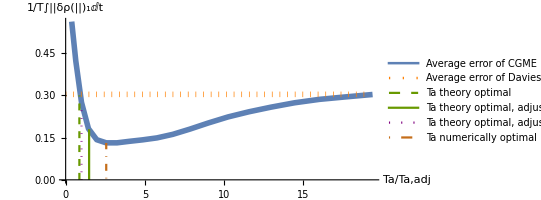

```mathematica
ListLinePlot[{avNoList,{{0,davNo},{19,davNo}},{{1/boostEffective ,0},{1/boostEffective ,0.3}},{{boostTypical/boostEffective ,0},{boostTypical/boostEffective ,0.18}},{{1,0},{1,0.25}},{{avNoList[[Ordering[avNoList[[;;,2]],1][[1]],1]],0.005},{avNoList[[Ordering[avNoList[[;;,2]],1][[1]],1]],0.131}}},PlotLegends->{"Average error of CGME","Average error of Davies","Ta theory optimal","Ta theory optimal, adjusted by typical norm of r.h.s.","Ta theory optimal, adjusted by true norm bound on r.h.s." ,"Ta numerically optimal"},AxesLabel->{"Ta/Ta,adj","1/T∫||δρ(||)_1ⅆt"},AxesStyle->Black,LabelStyle->Black,PlotStyle->{Thickness[0.01],{Dotted,Orange,Thickness[0.01]},{ colCll,Dashed}, colCll , {Purple,Dotted},DotDashed},AspectRatio->1/2]
```

we now compute the solution of CGME at the numerically optimal Ta again:

```mathematica
factorTave=avNoList[[Ordering[avNoList[[;;,2]],1][[1]],1]];
Tave = factorTave boostEffective Sqrt[t12 tbath/5]
factorTave boostEffective
```

2.86614

2.9552

```mathematica
filter2=(Sin[Tave(eps - omeg)/2])/(Tave(eps - omeg)/2);


Hls =Table[Sum[omP =Es[[k]]-Es[[i]]; om = Es[[j]]-Es[[k]];If[om +omP ==0,(1/(Tave  ))Re[NIntegrate[I(t-Tave) Exp[I om t ] corfunk,{t,0,Tave}]]Ainbasis[[i,k]]Ainbasis[[k,j]],(1/(Tave (om + omP) ))Re[NIntegrate[(Exp[I(om t - Tave (om +omP)/2)] - Exp[-I(omP t - Tave (om +omP)/2)])corfunk,{t,0,Tave}]]Ainbasis[[i,k]]Ainbasis[[k,j]]],{k,1,2^c}],{i,1,2^c},{j,1,2^c}];

zeMat={{0,0},{0,0}};
zeInit =At[zeMat,1];
termsC=I*(pMat[x].S.H.Sd -S.H.Sd.pMat[x])  ;
For[i=1,i<2^c +1,i++,
For[j=1,j<2^c +1,j++,
If[(i==j)&&(i<2^c),0,
a=zeInit;
If[(i==j)&&(i==2^c),For[m=1,m<2^c +1,m++,
a[[m,m]] = Ainbasis[[m,m]] ;
];,a[[i,j]] = Ainbasis[[i,j]] ;
];
ad = ConjugateTranspose[a];
For[k=1,k<2^c +1,k++,
For[l=1,l<2^c +1,l++,
If[(k==l )&&(k<2^c),0,
b=zeInit;

If[(k==l)&&(k==2^c),For[m=1,m<2^c +1,m++,
b[[m,m]] = Ainbasis[[m,m]] ;
];,b[[k,l]] = Ainbasis[[k,l]] ;
];
bd = ConjugateTranspose[b];



termsC=termsC+(1/(2))(NIntegrate[((SpDen/.dE->eps) Tave /(2  Pi))(filter2 /.omeg ->(Es[[j]]- Es[[i]]))(filter2 /.omeg ->(Es[[l]]- Es[[k]])),{eps,-Infinity,Infinity}])(2 a.pMat[x].bd  - bd.a.pMat[x] - pMat[x].bd. a   );
]]]
]]];



pIn =S.rhoIn.Sd;
s = NDSolve[{pMat'[x] == termsC+I*(pMat[x].Hls- Hls.pMat[x]), 
   pMat[0] == pIn}, {pMat}, {x, 0, timeConst t12}];
SolCfNewBasisOpt =pMat/.s[[1,1]];
denmatDif=SolORedfield[x t12]-SolCfNewBasisOpt[x t12];
traceNorm3=Re[Tr[MatrixPower[denmatDif.ConjugateTranspose[denmatDif ],1/2]]];





Plot[{traceNorm3,traceNorm2},{x,0,timeConst },PlotRange->All,PlotStyle->{colCll,colDav},PlotRange->All,AxesStyle->Black,AxesLabel->{"t","||δρ(||)_1"}]
```

-Graphics-

```mathematica
Tave=boostEffective Sqrt[tbath t12/5];
```

```mathematica
dfue[x_]:= (4t12 x/Tave) + (1-Exp[4x t12/t12effective])(4-8(Tave/t12effective)-(2Tave/t12effective)^2)/(4Tave/t12effective);
```

```mathematica
sod[j_]:=Table[{j i,j i,{0.01,0}},{i,-100,100}];pod[j_]:=Table[{j i/5,"",{0.005,0}},{i,-99,99}];ticksod[j_]:=ArrayFlatten[{{sod[j]},{pod[j]}}];
```

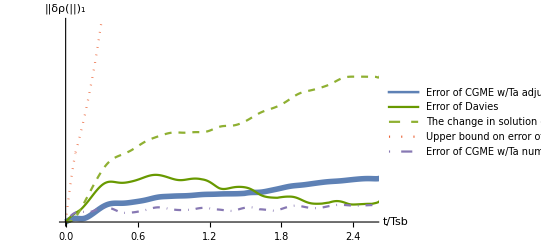

```mathematica
Plot[{traceNormSaved,traceNorm2,traceNormISca,(dfue[Min[x ,Tave/(2t12)]] + (Tave/t12effective))Max[Exp[4(t12 x -(Tave/2))/t12effective],1] -(Tave/t12effective) +(t12effective/t12)Exp[4x t12/t12effective] (1 - Max[Exp[-4x t12/t12effective],Exp[-2Tave/t12effective ] ])+Max[Exp[4(t12 x -(Tave/2))/t12effective]-1,0](tbath /Tave),traceNorm3},{x,0,3.74},PlotRange->{{0,timeConst},{0,2}},AxesStyle->Black,AxesLabel->{"t/Tsb","||δρ(||)_1"},Ticks->{Automatic,ticksod[0.25]},PlotStyle->{Thickness[0.01],colCll,Dashed, Dotted,DotDashed},PlotLegends->{"Error of CGME w/Ta adjusted by true norm of r.h.s","Error of Davies","The change in solution over time","Upper bound on error of CGME, adjusted by true norm of r.h.s." ,"Error of CGME w/Ta numerically optimal"}]
```

About norm of the r.h.s., we then illustrate the distribution with a Histogram,  where the early times give a small tail on the left:

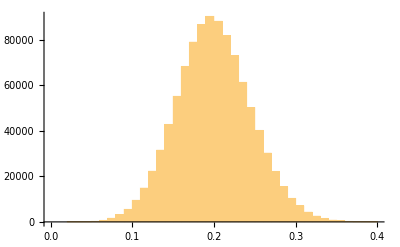

```mathematica
Histogram[Flatten[randNormTable4],{0,0.4, 0.01}]
```

```mathematica
listToPlot =HistogramList[Flatten[randNormTable4],{0,0.4, 0.01}];
typNorm =Mean[Flatten[randNormTable4]];
listAdjToPlot=N[{MovingAverage[listToPlot[[1]],2],listToPlot[[2]]}];
listAdjToPlot [[2]]= N[listToPlot[[2]]/10000];
hisHeight = Max[listAdjToPlot[[2]]];
listAdjToPlot=Transpose[listAdjToPlot];
p4=ListLinePlot[listAdjToPlot,Filling->Axis];
```

change the third one please

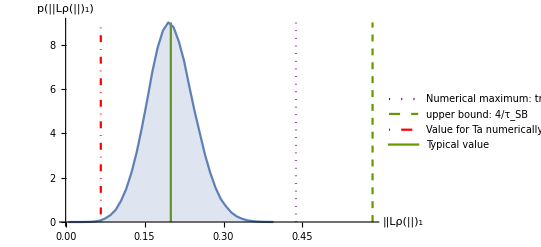

```mathematica
p5 =ListLinePlot[{{{Max[justmaxNormTable6],0},{Max[justmaxNormTable6],hisHeight}},{{4/t12,0},{4/t12,hisHeight}},{{4/(t12(factorTave boostEffective)^2),0},{4/(t12(factorTave boostEffective)^2),hisHeight}},{{typNorm ,0},{typNorm ,hisHeight}}},PlotLegends->{"Numerical maximum: true norm of r.h.s.", "upper bound: 4/τ_SB","Value for Ta numerically optimal","Typical value"},AxesStyle->Black,AxesLabel->{"||Lρ(||)_1","p(||Lρ(||)_1)"},PlotStyle->{{Purple,Dotted}, {colCll,Dashed},{Red,DotDashed},colCll}];
Show[p5,p4]
```